```mathematica
data1 = RandomVariate[NormalDistribution[1, 3], {30, 2}]
```

{{4.61977,-4.40538},{3.69091,-3.05425},{-2.09724,5.29895},{-3.17186,2.22969},{2.30057,0.270926},{2.08812,0.89788},{-1.39321,7.61659},{3.15299,-0.638497},{2.22238,5.32878},{0.593387,5.20575},{-1.51234,5.44015},{4.62856,0.419673},{3.83166,-1.92932},{1.49733,4.38085},{0.703489,1.78004},{-0.199803,2.26786},{-3.31306,5.10501},{4.73726,-1.03119},{-4.42512,-1.02568},{3.56021,2.21677},{-2.57225,4.93762},{5.60532,2.91716},{-2.14742,6.08588},{8.61372,-0.195296},{2.24749,1.25164},{2.20982,4.75892},{-4.68302,0.322766},{-0.144808,-2.02539},{0.475548,-1.20597},{0.343633,4.27601}}

```mathematica
data2 = RandomVariate[NormalDistribution[], {30, 2}]
```

{{-1.72938,0.282891},{0.767395,1.17827},{2.59108,1.22868},{-1.21368,0.804558},{0.496301,-0.522199},{0.50652,-0.213447},{-1.5793,-0.445133},{-0.433912,-0.421506},{0.837093,-1.00165},{-0.189691,-0.960461},{1.07857,-0.562583},{0.140193,-0.565635},{-0.036245,-1.37787},{0.372839,0.324528},{1.46015,-1.9072},{-1.23964,-1.44588},{-0.364975,0.00465371},{2.68544,-1.32661},{0.419593,-0.898536},{0.445931,0.481755},{1.71231,0.626988},{-0.863937,1.59415},{0.10071,-1.07574},{-0.72286,0.310017},{-0.223386,1.21088},{1.29943,-0.576876},{-1.72328,1.07314},{0.528366,0.489713},{-0.51626,0.516121},{0.000172541,-1.14181}}

```mathematica
data3 = RandomVariate[NormalDistribution[2, 5], {30, 2}]
```

{{2.38603,2.56321},{3.90326,0.678475},{8.0137,-3.38107},{-0.881162,4.75528},{-0.361439,1.96852},{2.96783,0.153512},{4.35494,-2.01391},{-0.179457,-7.34745},{7.61181,9.11069},{4.63265,6.58569},{-2.52919,11.2147},{0.146413,5.37741},{7.03816,4.43077},{-0.522169,4.88946},{1.92186,2.54879},{6.48365,4.84812},{-2.38312,1.71534},{6.29932,4.77204},{4.39903,4.10202},{-5.1041,4.62938},{-1.27215,3.17659},{-12.9598,2.92291},{-0.995805,1.64794},{5.75816,-0.952504},{7.18212,-2.85274},{5.526,6.47621},{-0.0526786,1.74503},{-6.55484,6.04589},{-7.17484,-3.27624},{1.31872,-4.28919}}

```mathematica
data = Join[data1, data2, data3]
```

{{4.61977,-4.40538},{3.69091,-3.05425},{-2.09724,5.29895},{-3.17186,2.22969},{2.30057,0.270926},{2.08812,0.89788},{-1.39321,7.61659},{3.15299,-0.638497},{2.22238,5.32878},{0.593387,5.20575},{-1.51234,5.44015},{4.62856,0.419673},{3.83166,-1.92932},{1.49733,4.38085},{0.703489,1.78004},{-0.199803,2.26786},{-3.31306,5.10501},{4.73726,-1.03119},{-4.42512,-1.02568},{3.56021,2.21677},{-2.57225,4.93762},{5.60532,2.91716},{-2.14742,6.08588},{8.61372,-0.195296},{2.24749,1.25164},{2.20982,4.75892},{-4.68302,0.322766},{-0.144808,-2.02539},{0.475548,-1.20597},{0.343633,4.27601},{-1.72938,0.282891},{0.767395,1.17827},{2.59108,1.22868},{-1.21368,0.804558},{0.496301,-0.522199},{0.50652,-0.213447},{-1.5793,-0.445133},{-0.433912,-0.421506},{0.837093,-1.00165},{-0.189691,-0.960461},{1.07857,-0.562583},{0.140193,-0.565635},{-0.036245,-1.37787},{0.372839,0.324528},{1.46015,-1.9072},{-1.23964,-1.44588},{-0.364975,0.00465371},{2.68544,-1.32661},{0.419593,-0.898536},{0.445931,0.481755},{1.71231,0.626988},{-0.863937,1.59415},{0.10071,-1.07574},{-0.72286,0.310017},{-0.223386,1.21088},{1.29943,-0.576876},{-1.72328,1.07314},{0.528366,0.489713},{-0.51626,0.516121},{0.000172541,-1.14181},{2.38603,2.56321},{3.90326,0.678475},{8.0137,-3.38107},{-0.881162,4.75528},{-0.361439,1.96852},{2.96783,0.153512},{4.35494,-2.01391},{-0.179457,-7.34745},{7.61181,9.11069},{4.63265,6.58569},{-2.52919,11.2147},{0.146413,5.37741},{7.03816,4.43077},{-0.522169,4.88946},{1.92186,2.54879},{6.48365,4.84812},{-2.38312,1.71534},{6.29932,4.77204},{4.39903,4.10202},{-5.1041,4.62938},{-1.27215,3.17659},{-12.9598,2.92291},{-0.995805,1.64794},{5.75816,-0.952504},{7.18212,-2.85274},{5.526,6.47621},{-0.0526786,1.74503},{-6.55484,6.04589},{-7.17484,-3.27624},{1.31872,-4.28919}}

```mathematica
FindClusters[data,3]
```

{{{4.61977,-4.40538},{3.69091,-3.05425},{2.30057,0.270926},{2.08812,0.89788},{3.15299,-0.638497},{4.62856,0.419673},{3.83166,-1.92932},{4.73726,-1.03119},{3.56021,2.21677},{5.60532,2.91716},{8.61372,-0.195296},{2.24749,1.25164},{2.59108,1.22868},{2.68544,-1.32661},{2.38603,2.56321},{3.90326,0.678475},{8.0137,-3.38107},{2.96783,0.153512},{4.35494,-2.01391},{7.61181,9.11069},{4.63265,6.58569},{7.03816,4.43077},{1.92186,2.54879},{6.48365,4.84812},{6.29932,4.77204},{4.39903,4.10202},{5.75816,-0.952504},{7.18212,-2.85274},{5.526,6.47621}},{{-2.09724,5.29895},{-3.17186,2.22969},{-1.39321,7.61659},{2.22238,5.32878},{0.593387,5.20575},{-1.51234,5.44015},{1.49733,4.38085},{-3.31306,5.10501},{-2.57225,4.93762},{-2.14742,6.08588},{2.20982,4.75892},{0.343633,4.27601},{-0.881162,4.75528},{-2.52919,11.2147},{0.146413,5.37741},{-0.522169,4.88946},{-5.1041,4.62938},{-1.27215,3.17659},{-12.9598,2.92291},{-6.55484,6.04589}},{{0.703489,1.78004},{-0.199803,2.26786},{-4.42512,-1.02568},{-4.68302,0.322766},{-0.144808,-2.02539},{0.475548,-1.20597},{-1.72938,0.282891},{0.767395,1.17827},{-1.21368,0.804558},{0.496301,-0.522199},{0.50652,-0.213447},{-1.5793,-0.445133},{-0.433912,-0.421506},{0.837093,-1.00165},{-0.189691,-0.960461},{1.07857,-0.562583},{0.140193,-0.565635},{-0.036245,-1.37787},{0.372839,0.324528},{1.46015,-1.9072},{-1.23964,-1.44588},{-0.364975,0.00465371},{0.419593,-0.898536},{0.445931,0.481755},{1.71231,0.626988},{-0.863937,1.59415},{0.10071,-1.07574},{-0.72286,0.310017},{-0.223386,1.21088},{1.29943,-0.576876},{-1.72328,1.07314},{0.528366,0.489713},{-0.51626,0.516121},{0.000172541,-1.14181},{-0.361439,1.96852},{-0.179457,-7.34745},{-2.38312,1.71534},{-0.995805,1.64794},{-0.0526786,1.74503},{-7.17484,-3.27624},{1.31872,-4.28919}}}

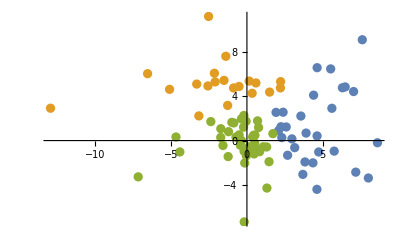

```mathematica
ListPlot[FindClusters[data, 3]]
```

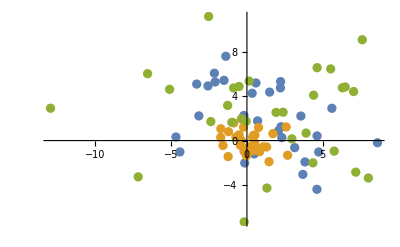

```mathematica
ListPlot[{data1, data2, data3}]
```

```mathematica
Needs["HierarchicalClustering`"]
```

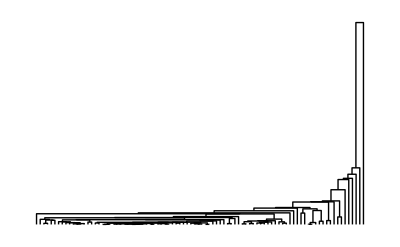

```mathematica
DendrogramPlot[data]
```

```mathematica
Agglomerate[data]
```

Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{4.61977,-4.40538},Cluster[Cluster[Cluster[Cluster[Cluster[{3.69091,-3.05425},Cluster[Cluster[{3.83166,-1.92932},{4.35494,-2.01391},0.280979,1,1],Cluster[{4.73726,-1.03119},{5.75816,-0.952504},1.04842,1,1],1.11191,2,2],1.28528,1,4],Cluster[Cluster[Cluster[Cluster[{2.68544,-1.32661},Cluster[{3.15299,-0.638497},Cluster[{2.96783,0.153512},Cluster[{2.30057,0.270926},Cluster[Cluster[{2.08812,0.89788},Cluster[{2.24749,1.25164},{2.59108,1.22868},0.11858,1,1],0.150545,1,2],{1.71231,0.626988},0.214615,3,1],0.438204,1,4],0.459027,1,5],0.661563,1,6],0.692102,1,7],Cluster[{3.90326,0.678475},{4.62856,0.419673},0.593035,1,1],1.15062,8,2],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{0.767395,1.17827},{0.703489,1.78004},0.366213,1,1],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{0.528366,0.489713},{0.445931,0.481755},0.00685888,1,1],{0.372839,0.324528},0.0300627,2,1],Cluster[Cluster[Cluster[Cluster[Cluster[{0.50652,-0.213447},{0.496301,-0.522199},0.0954324,1,1],{0.140193,-0.565635},0.128699,2,1],Cluster[Cluster[{0.419593,-0.898536},{0.475548,-1.20597},0.0976436,1,1],Cluster[Cluster[Cluster[{0.10071,-1.07574},{0.000172541,-1.14181},0.0144733,1,1],{-0.036245,-1.37787},0.057049,2,1],{-0.189691,-0.960461},0.0689372,3,1],0.133088,2,4],0.147513,3,6],{0.837093,-1.00165},0.17246,9,1],Cluster[{1.07857,-0.562583},{1.29943,-0.576876},0.0489799,1,1],0.251093,10,2],0.307287,3,12],Cluster[Cluster[{-0.433912,-0.421506},{-0.364975,0.00465371},0.186364,1,1],Cluster[{-0.72286,0.310017},{-0.51626,0.516121},0.0851623,1,1],0.221329,2,2],0.350117,15,4],{-0.144808,-2.02539},0.431064,19,1],Cluster[{-1.21368,0.804558},{-1.72328,1.07314},0.331825,1,1],0.485471,20,2],0.531241,2,22],{-1.72938,0.282891},0.538082,24,1],{-1.5793,-0.445133},0.552541,25,1],Cluster[Cluster[{-0.223386,1.21088},Cluster[{-0.0526786,1.74503},Cluster[{-0.361439,1.96852},{-0.199803,2.26786},0.115729,1,1],0.145281,1,2],0.31446,1,3],Cluster[{-0.863937,1.59415},{-0.995805,1.64794},0.0202829,1,1],0.392657,4,2],0.568462,26,6],{-2.38312,1.71534},0.84781,32,1],{-3.17186,2.22969},0.886678,33,1],{-1.23964,-1.44588},1.11685,34,1],1.19678,10,35],{1.46015,-1.9072},1.20822,45,1],1.67708,5,46],Cluster[Cluster[{2.38603,2.56321},{1.92186,2.54879},0.215657,1,1],{3.56021,2.21677},1.49872,2,1],1.7394,51,3],{-1.27215,3.17659},1.97572,54,1],Cluster[Cluster[Cluster[Cluster[Cluster[{-0.881162,4.75528},{-0.522169,4.88946},0.146881,1,1],Cluster[{0.146413,5.37741},{0.593387,5.20575},0.229253,1,1],0.685092,2,2],Cluster[Cluster[Cluster[{-1.51234,5.44015},Cluster[{-2.09724,5.29895},{-2.57225,4.93762},0.356192,1,1],0.362043,1,2],{-3.31306,5.10501},0.576823,3,1],{-2.14742,6.08588},0.621779,4,1],0.867433,4,5],{0.343633,4.27601},0.926794,9,1],Cluster[{1.49733,4.38085},Cluster[{2.20982,4.75892},{2.22238,5.32878},0.324901,1,1],0.650572,1,2],1.34202,10,3],2.64515,55,13],2.68834,1,68],{-1.39321,7.61659},2.91192,69,1],{-5.1041,4.62938},3.43402,70,1],{-6.55484,6.04589},4.11116,71,1],Cluster[Cluster[{4.39903,4.10202},{5.60532,2.91716},2.85904,1,1],Cluster[Cluster[Cluster[{6.29932,4.77204},{6.48365,4.84812},0.0397667,1,1],{7.03816,4.43077},0.48166,2,1],Cluster[{5.526,6.47621},{4.63265,6.58569},0.810066,1,1],3.50219,3,2],3.9222,2,5],4.25778,72,7],Cluster[{7.18212,-2.85274},{8.0137,-3.38107},0.970668,1,1],5.63856,79,2],{1.31872,-4.28919},5.69388,81,1],Cluster[{-4.68302,0.322766},{-4.42512,-1.02568},1.88482,1,1],5.91997,82,2],{8.61372,-0.195296},8.72757,84,1],{7.61181,9.11069},11.2911,85,1],{-0.179457,-7.34745},11.5975,86,1],{-7.17484,-3.27624},12.626,87,1],{-2.52919,11.2147},14.2367,88,1],{-12.9598,2.92291},50.7763,89,1]

```mathematica
DendrogramPlot[Agglomerate[data]]
```

-Graphics-

```mathematica
clu1 = DendrogramPlot[Agglomerate[data]]
```

-Graphics-

```mathematica
clu1 = Agglomerate[data]
```

Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{4.61977,-4.40538},Cluster[Cluster[Cluster[Cluster[Cluster[{3.69091,-3.05425},Cluster[Cluster[{3.83166,-1.92932},{4.35494,-2.01391},0.280979,1,1],Cluster[{4.73726,-1.03119},{5.75816,-0.952504},1.04842,1,1],1.11191,2,2],1.28528,1,4],Cluster[Cluster[Cluster[Cluster[{2.68544,-1.32661},Cluster[{3.15299,-0.638497},Cluster[{2.96783,0.153512},Cluster[{2.30057,0.270926},Cluster[Cluster[{2.08812,0.89788},Cluster[{2.24749,1.25164},{2.59108,1.22868},0.11858,1,1],0.150545,1,2],{1.71231,0.626988},0.214615,3,1],0.438204,1,4],0.459027,1,5],0.661563,1,6],0.692102,1,7],Cluster[{3.90326,0.678475},{4.62856,0.419673},0.593035,1,1],1.15062,8,2],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{0.767395,1.17827},{0.703489,1.78004},0.366213,1,1],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{0.528366,0.489713},{0.445931,0.481755},0.00685888,1,1],{0.372839,0.324528},0.0300627,2,1],Cluster[Cluster[Cluster[Cluster[Cluster[{0.50652,-0.213447},{0.496301,-0.522199},0.0954324,1,1],{0.140193,-0.565635},0.128699,2,1],Cluster[Cluster[{0.419593,-0.898536},{0.475548,-1.20597},0.0976436,1,1],Cluster[Cluster[Cluster[{0.10071,-1.07574},{0.000172541,-1.14181},0.0144733,1,1],{-0.036245,-1.37787},0.057049,2,1],{-0.189691,-0.960461},0.0689372,3,1],0.133088,2,4],0.147513,3,6],{0.837093,-1.00165},0.17246,9,1],Cluster[{1.07857,-0.562583},{1.29943,-0.576876},0.0489799,1,1],0.251093,10,2],0.307287,3,12],Cluster[Cluster[{-0.433912,-0.421506},{-0.364975,0.00465371},0.186364,1,1],Cluster[{-0.72286,0.310017},{-0.51626,0.516121},0.0851623,1,1],0.221329,2,2],0.350117,15,4],{-0.144808,-2.02539},0.431064,19,1],Cluster[{-1.21368,0.804558},{-1.72328,1.07314},0.331825,1,1],0.485471,20,2],0.531241,2,22],{-1.72938,0.282891},0.538082,24,1],{-1.5793,-0.445133},0.552541,25,1],Cluster[Cluster[{-0.223386,1.21088},Cluster[{-0.0526786,1.74503},Cluster[{-0.361439,1.96852},{-0.199803,2.26786},0.115729,1,1],0.145281,1,2],0.31446,1,3],Cluster[{-0.863937,1.59415},{-0.995805,1.64794},0.0202829,1,1],0.392657,4,2],0.568462,26,6],{-2.38312,1.71534},0.84781,32,1],{-3.17186,2.22969},0.886678,33,1],{-1.23964,-1.44588},1.11685,34,1],1.19678,10,35],{1.46015,-1.9072},1.20822,45,1],1.67708,5,46],Cluster[Cluster[{2.38603,2.56321},{1.92186,2.54879},0.215657,1,1],{3.56021,2.21677},1.49872,2,1],1.7394,51,3],{-1.27215,3.17659},1.97572,54,1],Cluster[Cluster[Cluster[Cluster[Cluster[{-0.881162,4.75528},{-0.522169,4.88946},0.146881,1,1],Cluster[{0.146413,5.37741},{0.593387,5.20575},0.229253,1,1],0.685092,2,2],Cluster[Cluster[Cluster[{-1.51234,5.44015},Cluster[{-2.09724,5.29895},{-2.57225,4.93762},0.356192,1,1],0.362043,1,2],{-3.31306,5.10501},0.576823,3,1],{-2.14742,6.08588},0.621779,4,1],0.867433,4,5],{0.343633,4.27601},0.926794,9,1],Cluster[{1.49733,4.38085},Cluster[{2.20982,4.75892},{2.22238,5.32878},0.324901,1,1],0.650572,1,2],1.34202,10,3],2.64515,55,13],2.68834,1,68],{-1.39321,7.61659},2.91192,69,1],{-5.1041,4.62938},3.43402,70,1],{-6.55484,6.04589},4.11116,71,1],Cluster[Cluster[{4.39903,4.10202},{5.60532,2.91716},2.85904,1,1],Cluster[Cluster[Cluster[{6.29932,4.77204},{6.48365,4.84812},0.0397667,1,1],{7.03816,4.43077},0.48166,2,1],Cluster[{5.526,6.47621},{4.63265,6.58569},0.810066,1,1],3.50219,3,2],3.9222,2,5],4.25778,72,7],Cluster[{7.18212,-2.85274},{8.0137,-3.38107},0.970668,1,1],5.63856,79,2],{1.31872,-4.28919},5.69388,81,1],Cluster[{-4.68302,0.322766},{-4.42512,-1.02568},1.88482,1,1],5.91997,82,2],{8.61372,-0.195296},8.72757,84,1],{7.61181,9.11069},11.2911,85,1],{-0.179457,-7.34745},11.5975,86,1],{-7.17484,-3.27624},12.626,87,1],{-2.52919,11.2147},14.2367,88,1],{-12.9598,2.92291},50.7763,89,1]

```mathematica
Length[clu1]
```

5

```mathematica
clu1[[-5]]
```

Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{4.61977,-4.40538},Cluster[Cluster[Cluster[Cluster[Cluster[{3.69091,-3.05425},Cluster[Cluster[{3.83166,-1.92932},{4.35494,-2.01391},0.280979,1,1],Cluster[{4.73726,-1.03119},{5.75816,-0.952504},1.04842,1,1],1.11191,2,2],1.28528,1,4],Cluster[Cluster[Cluster[Cluster[{2.68544,-1.32661},Cluster[{3.15299,-0.638497},Cluster[{2.96783,0.153512},Cluster[{2.30057,0.270926},Cluster[Cluster[{2.08812,0.89788},Cluster[{2.24749,1.25164},{2.59108,1.22868},0.11858,1,1],0.150545,1,2],{1.71231,0.626988},0.214615,3,1],0.438204,1,4],0.459027,1,5],0.661563,1,6],0.692102,1,7],Cluster[{3.90326,0.678475},{4.62856,0.419673},0.593035,1,1],1.15062,8,2],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{0.767395,1.17827},{0.703489,1.78004},0.366213,1,1],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{0.528366,0.489713},{0.445931,0.481755},0.00685888,1,1],{0.372839,0.324528},0.0300627,2,1],Cluster[Cluster[Cluster[Cluster[Cluster[{0.50652,-0.213447},{0.496301,-0.522199},0.0954324,1,1],{0.140193,-0.565635},0.128699,2,1],Cluster[Cluster[{0.419593,-0.898536},{0.475548,-1.20597},0.0976436,1,1],Cluster[Cluster[Cluster[{0.10071,-1.07574},{0.000172541,-1.14181},0.0144733,1,1],{-0.036245,-1.37787},0.057049,2,1],{-0.189691,-0.960461},0.0689372,3,1],0.133088,2,4],0.147513,3,6],{0.837093,-1.00165},0.17246,9,1],Cluster[{1.07857,-0.562583},{1.29943,-0.576876},0.0489799,1,1],0.251093,10,2],0.307287,3,12],Cluster[Cluster[{-0.433912,-0.421506},{-0.364975,0.00465371},0.186364,1,1],Cluster[{-0.72286,0.310017},{-0.51626,0.516121},0.0851623,1,1],0.221329,2,2],0.350117,15,4],{-0.144808,-2.02539},0.431064,19,1],Cluster[{-1.21368,0.804558},{-1.72328,1.07314},0.331825,1,1],0.485471,20,2],0.531241,2,22],{-1.72938,0.282891},0.538082,24,1],{-1.5793,-0.445133},0.552541,25,1],Cluster[Cluster[{-0.223386,1.21088},Cluster[{-0.0526786,1.74503},Cluster[{-0.361439,1.96852},{-0.199803,2.26786},0.115729,1,1],0.145281,1,2],0.31446,1,3],Cluster[{-0.863937,1.59415},{-0.995805,1.64794},0.0202829,1,1],0.392657,4,2],0.568462,26,6],{-2.38312,1.71534},0.84781,32,1],{-3.17186,2.22969},0.886678,33,1],{-1.23964,-1.44588},1.11685,34,1],1.19678,10,35],{1.46015,-1.9072},1.20822,45,1],1.67708,5,46],Cluster[Cluster[{2.38603,2.56321},{1.92186,2.54879},0.215657,1,1],{3.56021,2.21677},1.49872,2,1],1.7394,51,3],{-1.27215,3.17659},1.97572,54,1],Cluster[Cluster[Cluster[Cluster[Cluster[{-0.881162,4.75528},{-0.522169,4.88946},0.146881,1,1],Cluster[{0.146413,5.37741},{0.593387,5.20575},0.229253,1,1],0.685092,2,2],Cluster[Cluster[Cluster[{-1.51234,5.44015},Cluster[{-2.09724,5.29895},{-2.57225,4.93762},0.356192,1,1],0.362043,1,2],{-3.31306,5.10501},0.576823,3,1],{-2.14742,6.08588},0.621779,4,1],0.867433,4,5],{0.343633,4.27601},0.926794,9,1],Cluster[{1.49733,4.38085},Cluster[{2.20982,4.75892},{2.22238,5.32878},0.324901,1,1],0.650572,1,2],1.34202,10,3],2.64515,55,13],2.68834,1,68],{-1.39321,7.61659},2.91192,69,1],{-5.1041,4.62938},3.43402,70,1],{-6.55484,6.04589},4.11116,71,1],Cluster[Cluster[{4.39903,4.10202},{5.60532,2.91716},2.85904,1,1],Cluster[Cluster[Cluster[{6.29932,4.77204},{6.48365,4.84812},0.0397667,1,1],{7.03816,4.43077},0.48166,2,1],Cluster[{5.526,6.47621},{4.63265,6.58569},0.810066,1,1],3.50219,3,2],3.9222,2,5],4.25778,72,7],Cluster[{7.18212,-2.85274},{8.0137,-3.38107},0.970668,1,1],5.63856,79,2],{1.31872,-4.28919},5.69388,81,1],Cluster[{-4.68302,0.322766},{-4.42512,-1.02568},1.88482,1,1],5.91997,82,2],{8.61372,-0.195296},8.72757,84,1],{7.61181,9.11069},11.2911,85,1],{-0.179457,-7.34745},11.5975,86,1],{-7.17484,-3.27624},12.626,87,1],{-2.52919,11.2147},14.2367,88,1]

```mathematica
num = ClusterSplit[clu1,2]
```

{Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{4.61977,-4.40538},Cluster[Cluster[Cluster[Cluster[Cluster[{3.69091,-3.05425},Cluster[Cluster[{3.83166,-1.92932},{4.35494,-2.01391},0.280979,1,1],Cluster[{4.73726,-1.03119},{5.75816,-0.952504},1.04842,1,1],1.11191,2,2],1.28528,1,4],Cluster[Cluster[Cluster[Cluster[{2.68544,-1.32661},Cluster[{3.15299,-0.638497},Cluster[{2.96783,0.153512},Cluster[{2.30057,0.270926},Cluster[Cluster[{2.08812,0.89788},Cluster[{2.24749,1.25164},{2.59108,1.22868},0.11858,1,1],0.150545,1,2],{1.71231,0.626988},0.214615,3,1],0.438204,1,4],0.459027,1,5],0.661563,1,6],0.692102,1,7],Cluster[{3.90326,0.678475},{4.62856,0.419673},0.593035,1,1],1.15062,8,2],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{0.767395,1.17827},{0.703489,1.78004},0.366213,1,1],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{0.528366,0.489713},{0.445931,0.481755},0.00685888,1,1],{0.372839,0.324528},0.0300627,2,1],Cluster[Cluster[Cluster[Cluster[Cluster[{0.50652,-0.213447},{0.496301,-0.522199},0.0954324,1,1],{0.140193,-0.565635},0.128699,2,1],Cluster[Cluster[{0.419593,-0.898536},{0.475548,-1.20597},0.0976436,1,1],Cluster[Cluster[Cluster[{0.10071,-1.07574},{0.000172541,-1.14181},0.0144733,1,1],{-0.036245,-1.37787},0.057049,2,1],{-0.189691,-0.960461},0.0689372,3,1],0.133088,2,4],0.147513,3,6],{0.837093,-1.00165},0.17246,9,1],Cluster[{1.07857,-0.562583},{1.29943,-0.576876},0.0489799,1,1],0.251093,10,2],0.307287,3,12],Cluster[Cluster[{-0.433912,-0.421506},{-0.364975,0.00465371},0.186364,1,1],Cluster[{-0.72286,0.310017},{-0.51626,0.516121},0.0851623,1,1],0.221329,2,2],0.350117,15,4],{-0.144808,-2.02539},0.431064,19,1],Cluster[{-1.21368,0.804558},{-1.72328,1.07314},0.331825,1,1],0.485471,20,2],0.531241,2,22],{-1.72938,0.282891},0.538082,24,1],{-1.5793,-0.445133},0.552541,25,1],Cluster[Cluster[{-0.223386,1.21088},Cluster[{-0.0526786,1.74503},Cluster[{-0.361439,1.96852},{-0.199803,2.26786},0.115729,1,1],0.145281,1,2],0.31446,1,3],Cluster[{-0.863937,1.59415},{-0.995805,1.64794},0.0202829,1,1],0.392657,4,2],0.568462,26,6],{-2.38312,1.71534},0.84781,32,1],{-3.17186,2.22969},0.886678,33,1],{-1.23964,-1.44588},1.11685,34,1],1.19678,10,35],{1.46015,-1.9072},1.20822,45,1],1.67708,5,46],Cluster[Cluster[{2.38603,2.56321},{1.92186,2.54879},0.215657,1,1],{3.56021,2.21677},1.49872,2,1],1.7394,51,3],{-1.27215,3.17659},1.97572,54,1],Cluster[Cluster[Cluster[Cluster[Cluster[{-0.881162,4.75528},{-0.522169,4.88946},0.146881,1,1],Cluster[{0.146413,5.37741},{0.593387,5.20575},0.229253,1,1],0.685092,2,2],Cluster[Cluster[Cluster[{-1.51234,5.44015},Cluster[{-2.09724,5.29895},{-2.57225,4.93762},0.356192,1,1],0.362043,1,2],{-3.31306,5.10501},0.576823,3,1],{-2.14742,6.08588},0.621779,4,1],0.867433,4,5],{0.343633,4.27601},0.926794,9,1],Cluster[{1.49733,4.38085},Cluster[{2.20982,4.75892},{2.22238,5.32878},0.324901,1,1],0.650572,1,2],1.34202,10,3],2.64515,55,13],2.68834,1,68],{-1.39321,7.61659},2.91192,69,1],{-5.1041,4.62938},3.43402,70,1],{-6.55484,6.04589},4.11116,71,1],Cluster[Cluster[{4.39903,4.10202},{5.60532,2.91716},2.85904,1,1],Cluster[Cluster[Cluster[{6.29932,4.77204},{6.48365,4.84812},0.0397667,1,1],{7.03816,4.43077},0.48166,2,1],Cluster[{5.526,6.47621},{4.63265,6.58569},0.810066,1,1],3.50219,3,2],3.9222,2,5],4.25778,72,7],Cluster[{7.18212,-2.85274},{8.0137,-3.38107},0.970668,1,1],5.63856,79,2],{1.31872,-4.28919},5.69388,81,1],Cluster[{-4.68302,0.322766},{-4.42512,-1.02568},1.88482,1,1],5.91997,82,2],{8.61372,-0.195296},8.72757,84,1],{7.61181,9.11069},11.2911,85,1],{-0.179457,-7.34745},11.5975,86,1],{-7.17484,-3.27624},12.626,87,1],{-2.52919,11.2147},14.2367,88,1],{-12.9598,2.92291}}

```mathematica
Length[num]
```

2

```mathematica
num[[1]]
```

Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{4.61977,-4.40538},Cluster[Cluster[Cluster[Cluster[Cluster[{3.69091,-3.05425},Cluster[Cluster[{3.83166,-1.92932},{4.35494,-2.01391},0.280979,1,1],Cluster[{4.73726,-1.03119},{5.75816,-0.952504},1.04842,1,1],1.11191,2,2],1.28528,1,4],Cluster[Cluster[Cluster[Cluster[{2.68544,-1.32661},Cluster[{3.15299,-0.638497},Cluster[{2.96783,0.153512},Cluster[{2.30057,0.270926},Cluster[Cluster[{2.08812,0.89788},Cluster[{2.24749,1.25164},{2.59108,1.22868},0.11858,1,1],0.150545,1,2],{1.71231,0.626988},0.214615,3,1],0.438204,1,4],0.459027,1,5],0.661563,1,6],0.692102,1,7],Cluster[{3.90326,0.678475},{4.62856,0.419673},0.593035,1,1],1.15062,8,2],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{0.767395,1.17827},{0.703489,1.78004},0.366213,1,1],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{0.528366,0.489713},{0.445931,0.481755},0.00685888,1,1],{0.372839,0.324528},0.0300627,2,1],Cluster[Cluster[Cluster[Cluster[Cluster[{0.50652,-0.213447},{0.496301,-0.522199},0.0954324,1,1],{0.140193,-0.565635},0.128699,2,1],Cluster[Cluster[{0.419593,-0.898536},{0.475548,-1.20597},0.0976436,1,1],Cluster[Cluster[Cluster[{0.10071,-1.07574},{0.000172541,-1.14181},0.0144733,1,1],{-0.036245,-1.37787},0.057049,2,1],{-0.189691,-0.960461},0.0689372,3,1],0.133088,2,4],0.147513,3,6],{0.837093,-1.00165},0.17246,9,1],Cluster[{1.07857,-0.562583},{1.29943,-0.576876},0.0489799,1,1],0.251093,10,2],0.307287,3,12],Cluster[Cluster[{-0.433912,-0.421506},{-0.364975,0.00465371},0.186364,1,1],Cluster[{-0.72286,0.310017},{-0.51626,0.516121},0.0851623,1,1],0.221329,2,2],0.350117,15,4],{-0.144808,-2.02539},0.431064,19,1],Cluster[{-1.21368,0.804558},{-1.72328,1.07314},0.331825,1,1],0.485471,20,2],0.531241,2,22],{-1.72938,0.282891},0.538082,24,1],{-1.5793,-0.445133},0.552541,25,1],Cluster[Cluster[{-0.223386,1.21088},Cluster[{-0.0526786,1.74503},Cluster[{-0.361439,1.96852},{-0.199803,2.26786},0.115729,1,1],0.145281,1,2],0.31446,1,3],Cluster[{-0.863937,1.59415},{-0.995805,1.64794},0.0202829,1,1],0.392657,4,2],0.568462,26,6],{-2.38312,1.71534},0.84781,32,1],{-3.17186,2.22969},0.886678,33,1],{-1.23964,-1.44588},1.11685,34,1],1.19678,10,35],{1.46015,-1.9072},1.20822,45,1],1.67708,5,46],Cluster[Cluster[{2.38603,2.56321},{1.92186,2.54879},0.215657,1,1],{3.56021,2.21677},1.49872,2,1],1.7394,51,3],{-1.27215,3.17659},1.97572,54,1],Cluster[Cluster[Cluster[Cluster[Cluster[{-0.881162,4.75528},{-0.522169,4.88946},0.146881,1,1],Cluster[{0.146413,5.37741},{0.593387,5.20575},0.229253,1,1],0.685092,2,2],Cluster[Cluster[Cluster[{-1.51234,5.44015},Cluster[{-2.09724,5.29895},{-2.57225,4.93762},0.356192,1,1],0.362043,1,2],{-3.31306,5.10501},0.576823,3,1],{-2.14742,6.08588},0.621779,4,1],0.867433,4,5],{0.343633,4.27601},0.926794,9,1],Cluster[{1.49733,4.38085},Cluster[{2.20982,4.75892},{2.22238,5.32878},0.324901,1,1],0.650572,1,2],1.34202,10,3],2.64515,55,13],2.68834,1,68],{-1.39321,7.61659},2.91192,69,1],{-5.1041,4.62938},3.43402,70,1],{-6.55484,6.04589},4.11116,71,1],Cluster[Cluster[{4.39903,4.10202},{5.60532,2.91716},2.85904,1,1],Cluster[Cluster[Cluster[{6.29932,4.77204},{6.48365,4.84812},0.0397667,1,1],{7.03816,4.43077},0.48166,2,1],Cluster[{5.526,6.47621},{4.63265,6.58569},0.810066,1,1],3.50219,3,2],3.9222,2,5],4.25778,72,7],Cluster[{7.18212,-2.85274},{8.0137,-3.38107},0.970668,1,1],5.63856,79,2],{1.31872,-4.28919},5.69388,81,1],Cluster[{-4.68302,0.322766},{-4.42512,-1.02568},1.88482,1,1],5.91997,82,2],{8.61372,-0.195296},8.72757,84,1],{7.61181,9.11069},11.2911,85,1],{-0.179457,-7.34745},11.5975,86,1],{-7.17484,-3.27624},12.626,87,1],{-2.52919,11.2147},14.2367,88,1]

```mathematica
num//Length
```

2

```mathematica
Cases[num[[1]],{_,_},Infinity]//Length
```

89

```mathematica
data//Length
```

90

```mathematica
Cases[num[[2]],{_,_},Infinity]//Length
```

0

```mathematica
num[[2]]
```

{-12.9598,2.92291}

```mathematica
ClusterFlatten[num[[1]]]
```

{{4.61977,-4.40538},{3.69091,-3.05425},{3.83166,-1.92932},{4.35494,-2.01391},{4.73726,-1.03119},{5.75816,-0.952504},{2.68544,-1.32661},{3.15299,-0.638497},{2.96783,0.153512},{2.30057,0.270926},{2.08812,0.89788},{2.24749,1.25164},{2.59108,1.22868},{1.71231,0.626988},{3.90326,0.678475},{4.62856,0.419673},{0.767395,1.17827},{0.703489,1.78004},{0.528366,0.489713},{0.445931,0.481755},{0.372839,0.324528},{0.50652,-0.213447},{0.496301,-0.522199},{0.140193,-0.565635},{0.419593,-0.898536},{0.475548,-1.20597},{0.10071,-1.07574},{0.000172541,-1.14181},{-0.036245,-1.37787},{-0.189691,-0.960461},{0.837093,-1.00165},{1.07857,-0.562583},{1.29943,-0.576876},{-0.433912,-0.421506},{-0.364975,0.00465371},{-0.72286,0.310017},{-0.51626,0.516121},{-0.144808,-2.02539},{-1.21368,0.804558},{-1.72328,1.07314},{-1.72938,0.282891},{-1.5793,-0.445133},{-0.223386,1.21088},{-0.0526786,1.74503},{-0.361439,1.96852},{-0.199803,2.26786},{-0.863937,1.59415},{-0.995805,1.64794},{-2.38312,1.71534},{-3.17186,2.22969},{-1.23964,-1.44588},{1.46015,-1.9072},{2.38603,2.56321},{1.92186,2.54879},{3.56021,2.21677},{-1.27215,3.17659},{-0.881162,4.75528},{-0.522169,4.88946},{0.146413,5.37741},{0.593387,5.20575},{-1.51234,5.44015},{-2.09724,5.29895},{-2.57225,4.93762},{-3.31306,5.10501},{-2.14742,6.08588},{0.343633,4.27601},{1.49733,4.38085},{2.20982,4.75892},{2.22238,5.32878},{-1.39321,7.61659},{-5.1041,4.62938},{-6.55484,6.04589},{4.39903,4.10202},{5.60532,2.91716},{6.29932,4.77204},{6.48365,4.84812},{7.03816,4.43077},{5.526,6.47621},{4.63265,6.58569},{7.18212,-2.85274},{8.0137,-3.38107},{1.31872,-4.28919},{-4.68302,0.322766},{-4.42512,-1.02568},{8.61372,-0.195296},{7.61181,9.11069},{-0.179457,-7.34745},{-7.17484,-3.27624},{-2.52919,11.2147}}

```mathematica
ClusterFlatten[num[[2]]]
```

ClusterFlatten[{-12.9598,2.92291}]

```mathematica
ClusterFlatten[num]
```

ClusterFlatten[{Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{4.61977,-4.40538},Cluster[Cluster[Cluster[Cluster[Cluster[{3.69091,-3.05425},Cluster[Cluster[{3.83166,-1.92932},{4.35494,-2.01391},0.280979,1,1],Cluster[{4.73726,-1.03119},{5.75816,-0.952504},1.04842,1,1],1.11191,2,2],1.28528,1,4],Cluster[Cluster[Cluster[Cluster[{2.68544,-1.32661},Cluster[{3.15299,-0.638497},Cluster[{2.96783,0.153512},Cluster[{2.30057,0.270926},Cluster[Cluster[{2.08812,0.89788},Cluster[{2.24749,1.25164},{2.59108,1.22868},0.11858,1,1],0.150545,1,2],{1.71231,0.626988},0.214615,3,1],0.438204,1,4],0.459027,1,5],0.661563,1,6],0.692102,1,7],Cluster[{3.90326,0.678475},{4.62856,0.419673},0.593035,1,1],1.15062,8,2],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{0.767395,1.17827},{0.703489,1.78004},0.366213,1,1],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[{0.528366,0.489713},{0.445931,0.481755},0.00685888,1,1],{0.372839,0.324528},0.0300627,2,1],Cluster[Cluster[Cluster[Cluster[Cluster[{0.50652,-0.213447},{0.496301,-0.522199},0.0954324,1,1],{0.140193,-0.565635},0.128699,2,1],Cluster[Cluster[{0.419593,-0.898536},{0.475548,-1.20597},0.0976436,1,1],Cluster[Cluster[Cluster[{0.10071,-1.07574},{0.000172541,-1.14181},0.0144733,1,1],{-0.036245,-1.37787},0.057049,2,1],{-0.189691,-0.960461},0.0689372,3,1],0.133088,2,4],0.147513,3,6],{0.837093,-1.00165},0.17246,9,1],Cluster[{1.07857,-0.562583},{1.29943,-0.576876},0.0489799,1,1],0.251093,10,2],0.307287,3,12],Cluster[Cluster[{-0.433912,-0.421506},{-0.364975,0.00465371},0.186364,1,1],Cluster[{-0.72286,0.310017},{-0.51626,0.516121},0.0851623,1,1],0.221329,2,2],0.350117,15,4],{-0.144808,-2.02539},0.431064,19,1],Cluster[{-1.21368,0.804558},{-1.72328,1.07314},0.331825,1,1],0.485471,20,2],0.531241,2,22],{-1.72938,0.282891},0.538082,24,1],{-1.5793,-0.445133},0.552541,25,1],Cluster[Cluster[{-0.223386,1.21088},Cluster[{-0.0526786,1.74503},Cluster[{-0.361439,1.96852},{-0.199803,2.26786},0.115729,1,1],0.145281,1,2],0.31446,1,3],Cluster[{-0.863937,1.59415},{-0.995805,1.64794},0.0202829,1,1],0.392657,4,2],0.568462,26,6],{-2.38312,1.71534},0.84781,32,1],{-3.17186,2.22969},0.886678,33,1],{-1.23964,-1.44588},1.11685,34,1],1.19678,10,35],{1.46015,-1.9072},1.20822,45,1],1.67708,5,46],Cluster[Cluster[{2.38603,2.56321},{1.92186,2.54879},0.215657,1,1],{3.56021,2.21677},1.49872,2,1],1.7394,51,3],{-1.27215,3.17659},1.97572,54,1],Cluster[Cluster[Cluster[Cluster[Cluster[{-0.881162,4.75528},{-0.522169,4.88946},0.146881,1,1],Cluster[{0.146413,5.37741},{0.593387,5.20575},0.229253,1,1],0.685092,2,2],Cluster[Cluster[Cluster[{-1.51234,5.44015},Cluster[{-2.09724,5.29895},{-2.57225,4.93762},0.356192,1,1],0.362043,1,2],{-3.31306,5.10501},0.576823,3,1],{-2.14742,6.08588},0.621779,4,1],0.867433,4,5],{0.343633,4.27601},0.926794,9,1],Cluster[{1.49733,4.38085},Cluster[{2.20982,4.75892},{2.22238,5.32878},0.324901,1,1],0.650572,1,2],1.34202,10,3],2.64515,55,13],2.68834,1,68],{-1.39321,7.61659},2.91192,69,1],{-5.1041,4.62938},3.43402,70,1],{-6.55484,6.04589},4.11116,71,1],Cluster[Cluster[{4.39903,4.10202},{5.60532,2.91716},2.85904,1,1],Cluster[Cluster[Cluster[{6.29932,4.77204},{6.48365,4.84812},0.0397667,1,1],{7.03816,4.43077},0.48166,2,1],Cluster[{5.526,6.47621},{4.63265,6.58569},0.810066,1,1],3.50219,3,2],3.9222,2,5],4.25778,72,7],Cluster[{7.18212,-2.85274},{8.0137,-3.38107},0.970668,1,1],5.63856,79,2],{1.31872,-4.28919},5.69388,81,1],Cluster[{-4.68302,0.322766},{-4.42512,-1.02568},1.88482,1,1],5.91997,82,2],{8.61372,-0.195296},8.72757,84,1],{7.61181,9.11069},11.2911,85,1],{-0.179457,-7.34745},11.5975,86,1],{-7.17484,-3.27624},12.626,87,1],{-2.52919,11.2147},14.2367,88,1],{-12.9598,2.92291}}]